## Coupled Ring Oscillators: CelleratorML/CellzillaML example using Cellzilla2D

```mathematica
<<xlr8r.m
```

xlr8r 0.74 (13 May 2009) loaded 19 June 2009 at 14:24 GMT-06:60 using Mathematica 7.0 for Linux x86 (64-bit) (February 18, 2009) (Version 7., Release 1) (MathSBML 2.9.0 [8-Oct-2008])
GNU Lesser General Public License (LGPL) Terms Apply.

```mathematica
Get["Cellzilla2D.m"]
```

Cellzilla2D (0.15-α (19-Jun-09)) loaded Fri 19 Jun 2009 14:24:59 using xlr8r 0.74 (13 May 2009)

```mathematica
<<CelleratorML.m
```

CelleratorML 1.0.5 (19 June 2009) loaded 19 June 2009 at 14:25 GMT-06:60 using Mathematica Version 7.0 for Linux x86 (64-bit) (February 18, 2009) Release 1

## Generate the Ring Oscillator as an xlr8r model

```mathematica
reactions={{Underoverscript[X⟺XP, ZP, Z],MM[K,v,K,v]}, {Underoverscript[Y⟺YP, XP, X],MM[K,v,K,v]},
{Underoverscript[Z⟺ZP, YP, Y],MM[K,v,K,v]}};
someInitialConditions= {X-> 1, Y-> 2, Z-> 3};
someRateConstants={v-> 1, K-> .5};
```

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {XP,YP,ZP}

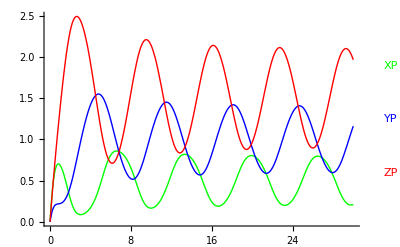

```mathematica
sim=run[reactions, timeSpan-> 30,initialConditions-> someInitialConditions, 
rates-> someRateConstants, plot-> True, plotVariables-> {XP, YP, ZP}];
```

## Save the model as CelleratorML

```mathematica
SaveModel["RingOscillator.xml", reactions, "Name"-> Ring, 
"Parameters"-> someRateConstants, "InitialConditions"-> someInitialConditions, "Descrioption"-> "Ring Oscillator based on Michaelis Menten Kinetics"]
```

RingOscillator.xml

## Read in the Cellerator ML and do a Simulation

```mathematica
{m, p, ics,  opts}=GetModel["RingOscillator.xml"]
```

Model: Ring

CelleratorML Version: 1.0

3 reactions

2 parameters

3 initial values

{{{(X⟺XP)_ZP^Z,MM[K,v,K,v]},{(Y⟺YP)_XP^X,MM[K,v,K,v]},{(Z⟺ZP)_YP^Y,MM[K,v,K,v]}},{v→1,K→0.5},{X→1,Y→2,Z→3},{Name→Ring,Frozen→{}}}

```mathematica
run[m, timeSpan-> 30,initialConditions-> ics, 
rates-> p, plot-> True, plotVariables-> {XP, YP, ZP}]
```

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {XP,YP,ZP}

-Graphics-

{{X→InterpolatingFunction[{{0.,30.}},<>],XP→InterpolatingFunction[{{0.,30.}},<>],Y→InterpolatingFunction[{{0.,30.}},<>],YP→InterpolatingFunction[{{0.,30.}},<>],Z→InterpolatingFunction[{{0.,30.}},<>],ZP→InterpolatingFunction[{{0.,30.}},<>]}}

## Generate a Cellzilla Template - based on centers

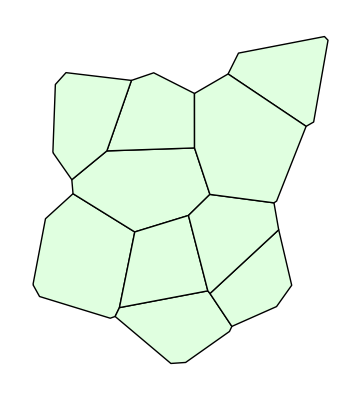

```mathematica
n=10; 
r:= RandomReal[{0, 100}]; 
centers=Table[{r,r}, {n}];
w=BoundedCellVoronoi[centers];
ShowTissue[w]
```

## Generate and Run a Cellerator System on the template using Cellzilla2D

```mathematica
bignet=CelleratorNetwork[m, {{X, DX}, {Y, DY}, {Z, DZ}}, w];
```

10 Cells.

6 internal reactions in each cell.

60 intracellular reactions.

102 diffusion reactions.

162 total reactions.

```mathematica
n=NTissueCells[w]
```

10

```mathematica
icOnTemplate={X-> Table[RandomReal[{0,3}], {n}], Y-> Table[RandomReal[{0,3}], {n}], Z-> Table[RandomReal[{0,3}], {n}], XP-> Table[0, {n}], YP-> Table[0, {n}], ZP-> Table[0, {n}]};
icOnTemplate=ListICToCellzillaIC[icOnTemplate];
```

```mathematica
czrates=Join[someRateConstants,{ DX-> 10, DY-> 11, DZ-> 9}]
```

{v→1,K→0.5,DX→10,DY→11,DZ→9}

```mathematica
sim=run[bignet,{0,30},MaxSteps-> 100000,rates->czrates,initialConditions->icOnTemplate];
```

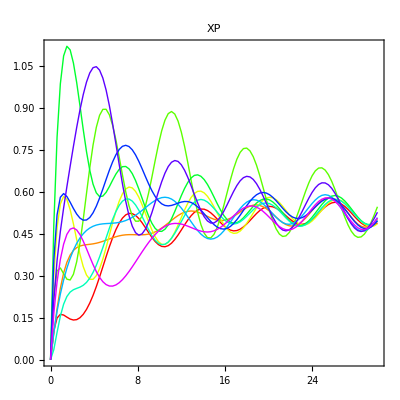

```mathematica
SimPlot[sim, XP]
```

## Save the Cellzilla Model

```mathematica
SaveCellzillaModel["Multiple-Ring-OScillators.xml", 
"Models"-> {"RingOscillator.xml"},
"Tissue"-> w,
"Parameters"-> {DX-> 10, DY-> 11, DZ-> 9}, 
"InitialConditions"-> icOnTemplate, 
"DiffusingSpecies"-> {{X, DX}, {Y, DY}, {Z, DZ}}
]
```

Model name: CellzillaModel

Model file name(s) or URL(s):

RingOscillator.xml

3 Diffusing Species

3 Parameters

60 Initial Conditions

2-D tissue: 36 vertices; 45 edges; 10 cells.

Multiple-Ring-OScillators.xml

## Recover the CellzillaML and run a simulation based on it

```mathematica
czm=GetCellzillaModel["Multiple-Ring-OScillators.xml", "Quiet"-> False]
```

File: Multiple-Ring-OScillators.xml

CellzillaML version: 1.0

Creation Date: 2009-06-19T14:38:08

Mathematica: Version 7. release 1 on Linux x86 (64-bit)

Model Name: CellzillaModel

⟶ Importing CelleratorML file: RingOscillator.xml

Model: Ring

CelleratorML Version: 1.0

3 reactions

2 parameters

3 initial values

Circuits: {{(X⟺XP)_ZP^Z,MM[K,v,K,v]},{(Y⟺YP)_XP^X,MM[K,v,K,v]},{(Z⟺ZP)_YP^Y,MM[K,v,K,v]}}

local parameters (may be superceded): {v→1,K→0.5}

frozenVariables from models: {}

Global parameters: {DX→10,DY→11,DZ→9}

Joined parameters: {DX→10,DY→11,DZ→9,K→0.5,v→1}

ic: {X→{0.599876,0.550784,0.893646,0.966048,2.3262,0.0776449,0.973564,1.4849,2.32472,0.271354},XP→{0,0,0,0,0,0,0,0,0,0},Y→{1.78427,0.0414888,1.14711,2.51936,1.46287,0.330976,1.70287,2.6607,1.47518,0.183211},YP→{0,0,0,0,0,0,0,0,0,0},Z→{0.871218,0.569884,1.97235,1.54576,2.28383,0.242789,0.552997,2.16303,1.01553,1.88976},ZP→{0,0,0,0,0,0,0,0,0,0}}

Diffusing Species: {{X,DX},{Y,DY},{Z,DZ}}

{Circuit→{{(X⟺XP)_ZP^Z,MM[K,v,K,v]},{(Y⟺YP)_XP^X,MM[K,v,K,v]},{(Z⟺ZP)_YP^Y,MM[K,v,K,v]}},Parameters→{DX→10,DY→11,DZ→9,K→0.5,v→1},IC→{X→{0.599876,0.550784,0.893646,0.966048,2.3262,0.0776449,0.973564,1.4849,2.32472,0.271354},XP→{0,0,0,0,0,0,0,0,0,0},Y→{1.78427,0.0414888,1.14711,2.51936,1.46287,0.330976,1.70287,2.6607,1.47518,0.183211},YP→{0,0,0,0,0,0,0,0,0,0},Z→{0.871218,0.569884,1.97235,1.54576,2.28383,0.242789,0.552997,2.16303,1.01553,1.88976},ZP→{0,0,0,0,0,0,0,0,0,0}},DiffusingSpecies→{{X,DX},{Y,DY},{Z,DZ}},Tissue→Tissue[{{-15.1489,17.9328},{-12.6454,13.4125},{-10.3737,43.0588},{-7.552,68.3021},{-6.6024,94.2432},{-2.54346,98.7573},{-0.322418,57.9477},{0.138209,52.6075},{13.0496,68.9258},{14.3449,5.13868},{16.2185,5.80217},{17.8592,9.1783},{22.4396,95.794},{23.7131,38.0252},{30.9379,98.6943},{37.501,-12.1138},{43.1229,-11.7313},{44.2061,44.3109},{46.5077,90.8239},{46.5272,70.0534},{51.6086,15.5677},{52.4026,52.3391},{52.4206,14.5621},{59.3281,98.2474},{59.8668,0.0840303},{60.7868,2.01843},{63.3031,106.202},{76.8554,49.1176},{77.8368,9.57391},{77.8689,49.8138},{78.6569,38.8511},{83.6214,17.702},{89.1234,78.2879},{92.0008,79.9343},{96.1321,112.522},{97.4868,111.11}},{{1,2},{1,3},{2,10},{3,8},{4,5},{4,7},{5,6},{6,13},{7,8},{7,9},{8,14},{9,13},{9,20},{10,11},{11,12},{11,16},{12,14},{12,21},{13,15},{14,18},{15,19},{16,17},{17,25},{18,21},{18,22},{19,20},{19,24},{20,22},{21,23},{22,28},{23,26},{23,31},{24,27},{24,33},{25,26},{26,29},{27,35},{28,30},{28,31},{29,32},{30,33},{31,32},{33,34},{34,36},{35,36}},{{2,1,3,14,15,17,11,4},{10,9,11,20,25,28,13},{15,16,22,23,35,31,29,18},{33,34,43,44,45,37},{31,36,40,42,32},{17,18,24,20},{12,13,26,21,19},{24,29,32,39,30,25},{26,28,30,38,41,34,27},{5,6,10,12,8,7}}]}

```mathematica
ShowTissue[w]
```

-Graphics-

```mathematica
par="Parameters"/.czm
```

{DX→10,DY→11,DZ→9,K→0.5,v→1}

```mathematica
myic=ListICToCellzillaIC["IC"/.czm]
```

{X[1]→0.599876,X[2]→0.550784,X[3]→0.893646,X[4]→0.966048,X[5]→2.3262,X[6]→0.0776449,X[7]→0.973564,X[8]→1.4849,X[9]→2.32472,X[10]→0.271354,XP[1]→0,XP[2]→0,XP[3]→0,XP[4]→0,XP[5]→0,XP[6]→0,XP[7]→0,XP[8]→0,XP[9]→0,XP[10]→0,Y[1]→1.78427,Y[2]→0.0414888,Y[3]→1.14711,Y[4]→2.51936,Y[5]→1.46287,Y[6]→0.330976,Y[7]→1.70287,Y[8]→2.6607,Y[9]→1.47518,Y[10]→0.183211,YP[1]→0,YP[2]→0,YP[3]→0,YP[4]→0,YP[5]→0,YP[6]→0,YP[7]→0,YP[8]→0,YP[9]→0,YP[10]→0,Z[1]→0.871218,Z[2]→0.569884,Z[3]→1.97235,Z[4]→1.54576,Z[5]→2.28383,Z[6]→0.242789,Z[7]→0.552997,Z[8]→2.16303,Z[9]→1.01553,Z[10]→1.88976,ZP[1]→0,ZP[2]→0,ZP[3]→0,ZP[4]→0,ZP[5]→0,ZP[6]→0,ZP[7]→0,ZP[8]→0,ZP[9]→0,ZP[10]→0}

```mathematica
bignet=CelleratorNetwork["Circuit"/.czm, "DiffusingSpecies"/.czm, w];
```

10 Cells.

6 internal reactions in each cell.

60 intracellular reactions.

102 diffusion reactions.

162 total reactions.

```mathematica
sim=RunSim[bignet, 
"Parameters"/.czm, 
ListICToCellzillaIC["IC"/.czm], {0, 30} ];
```

```mathematica
SimPlot[sim, XP]
```

-Graphics-